Домашняя работа по Компьютерному практикуму по математике.
Корнеев А.В. БПМ 151.
Вариант 11.

Задание 1.

Исходное уравнение:

d^2/dt^2 y + ∂/(∂y)U(y)==0, U(y)=y^3/3*(y^2/4-1)
Умножим исходное уравнение на y' и преобразуем.
y''*y'+U'_y*y'==0
Получим 
d/dt(y'^2/2+U)==0

y'^2/2+U == E, это сумма соответсвенно кинетической и потенциальной энергии

Построим график U(y). По графику можно сразу понять, где находятся точки равновесия.

```mathematica
U[y_]=y^3/3*(y^2/4-1)
```

1/3 y^3 (-1+y^2/4)

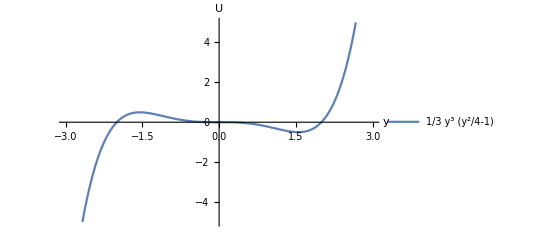

```mathematica
fig01 = Plot[U[y],{y,-3,3},PlotRange->{-5,5},AxesLabel->{y,U},PlotLegends->{U[y]}]
```

Точки равновесия находятся в y: U'_y == 0
Вот они:

```mathematica
sol1 = Solve[D[U[y],y]==0,y]
```

{{y→0},{y→0},{y→-2 √(3/5)},{y→2 √(3/5)}}

```mathematica
tempfig1 = ContourPlot[x==-2 √(3/5),{x,-5,5},{y,0,(16 √(3/5))/25},ContourStyle->Directive[RGBColor[0.05,0.05,0.05],Opacity[0.994],AbsoluteThickness[1.8800000000000001],Dashed]];
tempfig2 = ContourPlot[x==2 √(3/5),{x,-5,5},{y,0,-(16 √(3/5))/25},ContourStyle->Directive[RGBColor[0.05,0.05,0.05],Opacity[0.994],AbsoluteThickness[1.8800000000000001],Dashed]];
```

```mathematica
tempfig3 =ContourPlot[{y==(16 √(3/5))/25,y==-(16 √(3/5))/25},{x,-5,5},{y,-0.5,0.5},ContourStyle->Directive[RGBColor[0.05,0.05,0.05],Opacity[0.994],AbsoluteThickness[1.8800000000000001],Dashed]];
```

```mathematica
Show[fig01,tempfig1,tempfig2,tempfig3];
```

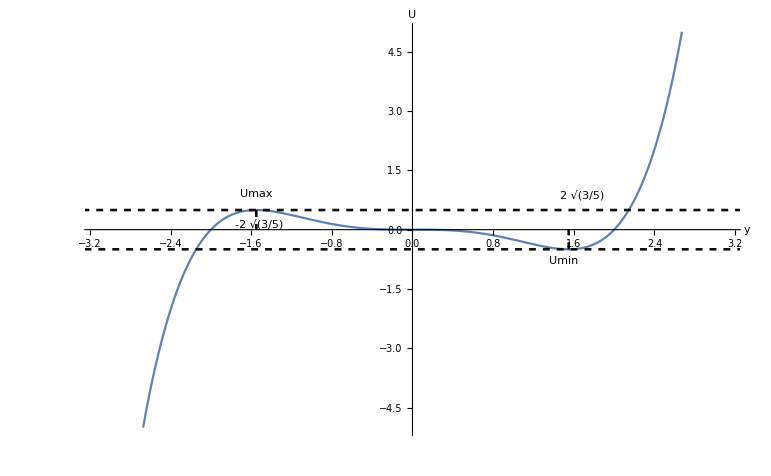

Umax, Umin - энергии в точках -2 √(3/5) и 2 √(3/5) соответственно

```mathematica
Umax = U[-2 √(3/5)]
```

(16 √(3/5))/25

```mathematica
Umin = U[2 √(3/5)]
```

-(16 √(3/5))/25

```mathematica
N[-(16 √(3/5))/25]
```

-0.495742

Построим фазовый портрет при различных значениях полной энергии  Е

```mathematica
ContourPlot[Evaluate@Table[y^2/2+x^3/3*(x^2/4-1)==Energy,{Energy,{-0.4,-0.1,0.4,0.1,0.8,-0.8,(16 √(3/5))/25,-(16 √(3/5))/25}}],{x,-5,5},{y,-5,5},PlotLegends->{"E=-0.4","E=-0.1","E=0.4","E=0.1","E=0.8","E=-0.8","E=(16 SqrtBox[FractionBox[3, 5]])/25","E=-(16 SqrtBox[FractionBox[3, 5]])/25"},PlotTheme->"Scientific",Axes->True,AxesStyle->Arrowheads[{0.0,0.05}],AxesLabel->{y,y'},LabelStyle->Directive[Large]];
```

-Graphics-

```mathematica
Manipulate[ContourPlot[{y^2/2+x^3/3*(x^2/4-1)==Energy},{x,-5,5},{y,-5,5}],{Energy,-(16 √(3/5))/25-0.1,(16 √(3/5))/25+0.1}]
```

a) Финитное движение возможно в интервале (Umin, Umax) = (-(16 √(3/5))/25,(16 √(3/5))/25)
	1. Найдем максимальное и минимальное отклонение от начала координат ymax и ymin, которые очевидно достигаются при U=Umax

```mathematica
Solve[U[y]==(16 √(3/5))/25,y]
```

{{y→-2 √(3/5)},{y→-2 √(3/5)},{y→2 (2^(1/3)/(√3 5^(1/6))+2/(√15))},{y→4/(√15)-(2^(1/3) (1-ⅈ √3))/(√3 5^(1/6))},{y→4/(√15)-(2^(1/3) (1+ⅈ √3))/(√3 5^(1/6))}}

```mathematica
ymax = 2 (2^(1/3)/(√3 5^(1/6))+2/(√15));
```

```mathematica
N[ymax]
```

2.14534

```mathematica
ymin = -2 √(3/5);
```

```mathematica
N[ymin]
```

-1.54919

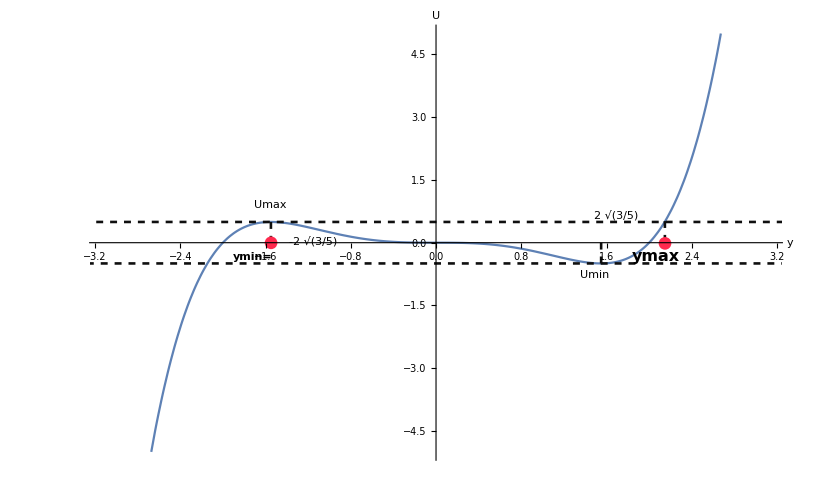

2. Значение энергии соответсвующее точке 0.5*ymax E2 = -0.293068 - отрицательное, и, как видно из графика выше, оно не может быть “максимальным удалением”, однако, его можно положить минимальным, а в качестве максимального удаления взять другой корень уравнения U[y]==E2: y=1.85784

```mathematica
Solve[U[y]==Umin,y]
```

{{y→2 √(3/5)},{y→2 √(3/5)},{y→2 (-2^(1/3)/(√3 5^(1/6))-2/(√15))},{y→-4/(√15)+(2^(1/3) (1-ⅈ √3))/(√3 5^(1/6))},{y→-4/(√15)+(2^(1/3) (1+ⅈ √3))/(√3 5^(1/6))}}

```mathematica
N[2 (-2^(1/3)/(√3 5^(1/6))-2/(√15))]
```

-2.14534

```mathematica
E2 = U[0.5*ymax]
```

-0.293068

```mathematica
N[0.5*ymax]
```

1.07267

```mathematica
Solve[U[y]==E2,y]
```

{{y→-2.09362},{y→-0.418447-0.817194 ⅈ},{y→-0.418447+0.817194 ⅈ},{y→1.07267},{y→1.85784}}

```mathematica
ymin1= 1.072670424493324;
```

```mathematica
ymax1=1.8578389038186072;
```

y'^2/2+ U[y] = E
y’=±√(2*(E-U[y]))

Знак «+» в этом уравнении соответствует участкам фазовых траекторий, лежащим в
верхней полуплоскости, знак «–» — в нижней.

dt =± dy/(√(2*(E-U[y])))
T = 2*∫_ymin^ymax dy/(√(2*(E-U[y])))

```mathematica
ymin
```

-2 √(3/5)

```mathematica
N[ymin]
```

-1.54919

```mathematica
N[ymax]
```

2.14534

```mathematica
T=2*NIntegrate[1/Sqrt[2*(E2-U[y])],{y,ymin1,ymax1}]
```

4.05818

```mathematica
2*NIntegrate[1/Sqrt[2*(Umin-U[y])],{y,-Infinity,-2.1453408489866477}]
```

1.77491

```mathematica
Solve[U[y]==Umax+1,y]
```

{{y→Root[{-3+5 #1^2&,-300-192 #1-100 #2^3+25 #2^5&},{2,1}]},{y→Root[{-3+5 #1^2&,-300-192 #1-100 #2^3+25 #2^5&},{2,2}]},{y→Root[{-3+5 #1^2&,-300-192 #1-100 #2^3+25 #2^5&},{2,3}]},{y→Root[{-3+5 #1^2&,-300-192 #1-100 #2^3+25 #2^5&},{2,4}]},{y→Root[{-3+5 #1^2&,-300-192 #1-100 #2^3+25 #2^5&},{2,5}]}}

```mathematica
N[%199]
```

{{y→2.32847},{y→-1.77199-0.656321 ⅈ},{y→-1.77199+0.656321 ⅈ},{y→0.607756-1.3377 ⅈ},{y→0.607756+1.3377 ⅈ}}

```mathematica
NIntegrate[1/Sqrt[2*(Umax+1-U[y])],{y,-Infinity,2.328467897949097}]
```

3.38187

```mathematica
NIntegrate[1/Sqrt[2*(Umax-U[y])],{y,-Infinity,ymin}]
```

21.4946

```mathematica
NIntegrate[1/Sqrt[2*(Umax-U[y])],{y,ymin,ymax}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {-1.5491933384829593507838783507203121434798917666531510231716847748}. NIntegrate obtained 26.725 and 1.65493 for the integral and error estimates.

26.725

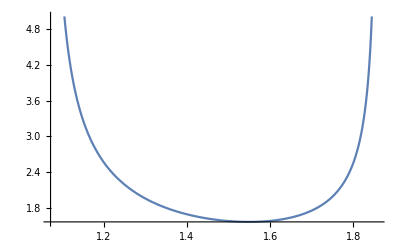

```mathematica
Plot[1/Sqrt[2*(E2-U[y])],{y,ymin1,ymax1}]
```

*******
б) Диапазон энергий, при которых траектория уходит на +∞ или −∞ - это интервалы (Umax, +∞) (-∞,Umin). Для этих диапазонов энергий бесконечно удаленная точка траектории достигается за бесконечное время.

-Graphics-
-Graphics-

Траектории стремятся к конечному значению за
бесконечное время при значении энергии равном Umax.

-Graphics-

Задача 2.

Исходная система:
Piecewise[{{x' = siny, }, {y' = -sinx, }}]
Рассмотрим квадрат {x, 0, 2π }, {y, 0, 2π }, в нем 9 особых точек:
(0, 0)
(0, π)
(0,2π)
(π, 0)
(π, π)
(π,2π)
(2π,0)
(2π,π)
(2π,2π)

Построим фазовый портрет системы.
dy/dx=-sinx/siny
siny dy =-sinx dx
-cosy +C = cosx

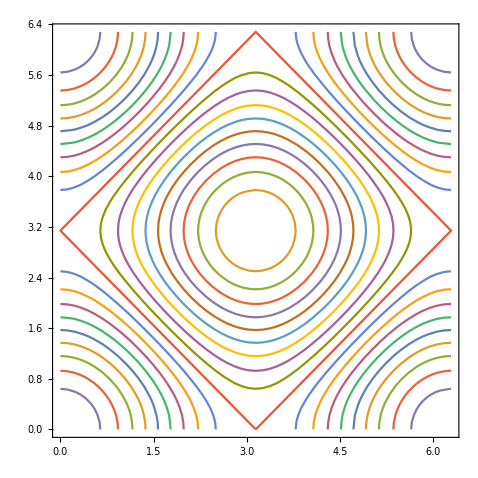

```mathematica
fig211 = ContourPlot[Evaluate@Table[-Cos[y]+P==Cos[x],{P,Table[x,{x,-2,2,0.2}]}],{x,0,2Pi},{y,0,2Pi}]
```

Линеаризуем систему вблизи особых точек. 

1) x_0=0 y_0=0

Piecewise[{{x' = y, }, {y' = -x, }}]
det(-λ | 1
-1 | -λ)=λ^2+1=0
λ_(1,2)=±i
Тип особой точки - центр.

2) x_0=0 y_0=π

Piecewise[{{x' = -y, }, {y' = -x, }}]
det(-λ | -1
-1 | -λ)=λ^2-1=0
λ_(1,2)=±1
Тип особой точки -седло.

3) x_0=0 y_0=2π Аналогично случаю 1)
Тип особой точки - центр.

4) x_0=π y_0=0

Piecewise[{{x' = y, }, {y' = x, }}]
det(-λ | 1
1 | -λ)=λ^2-1=0
λ_(1,2)=±1
Тип особой точки -седло.

5)x_0=π y_0=π

Piecewise[{{x' = -y, }, {y' = x, }}]
det(-λ | -1
1 | -λ)=λ^2+1=0
λ_(1,2)=±i
Тип особой точки -центр.

6) x_0=2π y_0=π Аналогично случаю 2)
Тип особой точки -седло.

7) x_0=0 y_0=2π  Аналогично случаю 1)
Тип особой точки - центр.

8) x_0=π y_0=2π  Аналогично случаю 2)
Тип особой точки -седло.

9) x_0=2π y_0=2π  Аналогично случаю 1)
Тип особой точки -центр.

Выясним направление траекторий в каждой из областей рассматриваесого квадрата, отделенной сепаратрисами y=±x+const (на рисунке изображены красным)

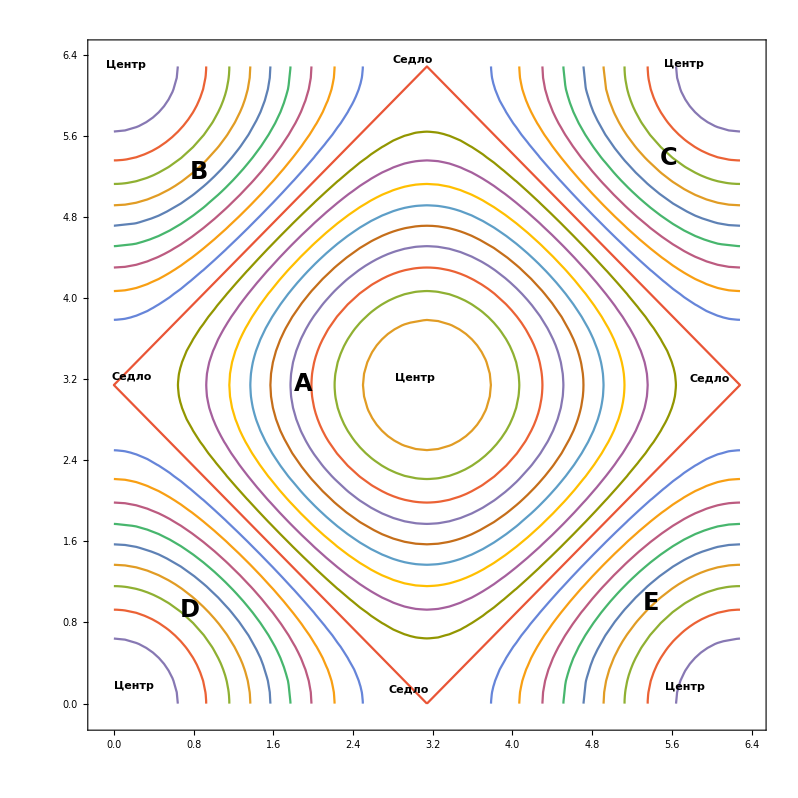

```mathematica
Sin[Pi/2]
```

1

```mathematica
Grid[{{"Область А", "Область B","Область C","Область D","Область E"},{"x=π y=(3  π)/2 \nx'=-1 y'=0","x=0 y=(3  π)/2 \nx'=-1 y'=0","x=2π y=(3  π)/2 \nx'=-1 y'=0","x=0 y=π/2 \nx'=1 y'=0","x=2π y=π/2 \nx'=1 y'=0"}},Frame->All]
```

Область А | Область B | Область C | Область D | Область E
x=π y=(3  π)/2 
x'=-1 y'=0 | x=0 y=(3  π)/2 
x'=-1 y'=0 | x=2π y=(3  π)/2 
x'=-1 y'=0 | x=0 y=π/2 
x'=1 y'=0 | x=2π y=π/2 
x'=1 y'=0

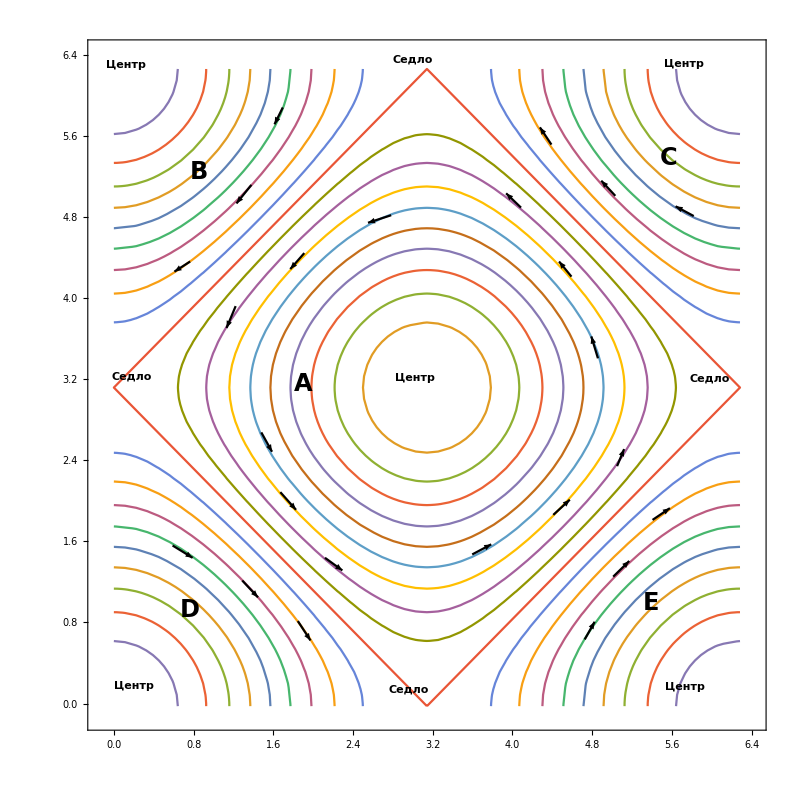

Задача 3

```mathematica
Clear[x]
```

Задано следующее рекурентное соотношение :
a[n+1]=1-μ*a[n]^2

```mathematica
f[x_,μ_]=1-μ*x^2
```

1-x^2 μ

```mathematica
Manipulate[Plot[{x,f[x,μ]},{x,-10,10}],{μ,1/4,2}]
```

```mathematica
seq1=RecurrenceTable[{a1[n+1]==1-μ*a1[n]^2,a1[1]==0.1}/.μ->1.74,a1,{n,1,1000}];
```

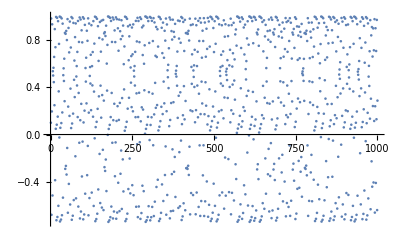

```mathematica
ListPlot[seq1]
```

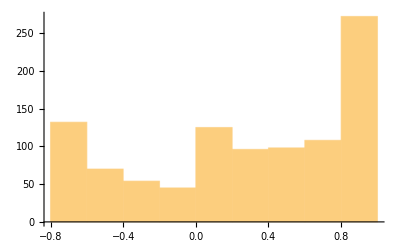

```mathematica
Histogram[seq1]
```

```mathematica
seq2 = RecurrenceTable[{a2[n+1]==1-μ*a2[n]^2,a2[1]==0.1}/.μ->1.75,a2,{n,1,1000}];
```

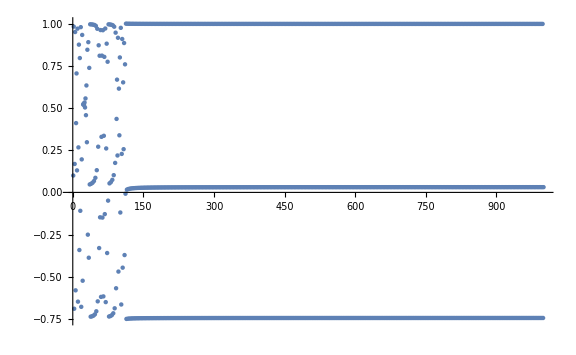

```mathematica
ListPlot[seq2]
```

```mathematica
Table[seq2[[i]],{i,200,253}]
```

{0.998472,-0.744654,0.0296073,0.998466,-0.744635,0.0296578,0.998461,-0.744617,0.0297054,0.998456,-0.744599,0.0297506,0.998451,-0.744583,0.0297933,0.998447,-0.744567,0.0298339,0.998442,-0.744553,0.0298724,0.998438,-0.744539,0.0299091,0.998435,-0.744525,0.029944,0.998431,-0.744512,0.0299774,0.998427,-0.7445,0.0300092,0.998424,-0.744488,0.0300396,0.998421,-0.744477,0.0300687,0.998418,-0.744467,0.0300966,0.998415,-0.744456,0.0301233,0.998412,-0.744446,0.030149,0.998409,-0.744437,0.0301736,0.998407,-0.744428,0.0301973}

```mathematica
Table[seq2[[i]],{i,800,853}]
```

{0.998304,-0.744068,0.031135,0.998304,-0.744068,0.0311362,0.998303,-0.744067,0.0311373,0.998303,-0.744067,0.0311384,0.998303,-0.744066,0.0311395,0.998303,-0.744066,0.0311406,0.998303,-0.744065,0.0311417,0.998303,-0.744065,0.0311428,0.998303,-0.744065,0.0311438,0.998303,-0.744064,0.0311449,0.998302,-0.744064,0.031146,0.998302,-0.744063,0.031147,0.998302,-0.744063,0.031148,0.998302,-0.744063,0.0311491,0.998302,-0.744062,0.0311501,0.998302,-0.744062,0.0311511,0.998302,-0.744061,0.0311521,0.998302,-0.744061,0.0311531}

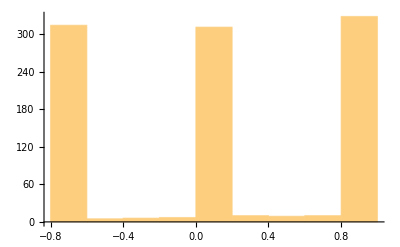

```mathematica
Histogram[seq2]
```

```mathematica
seq3 = RecurrenceTable[{a3[n+1]==1-μ*a3[n]^2,a3[1]==0.1}/.μ->1.76,a3,{n,1,1000}];
```

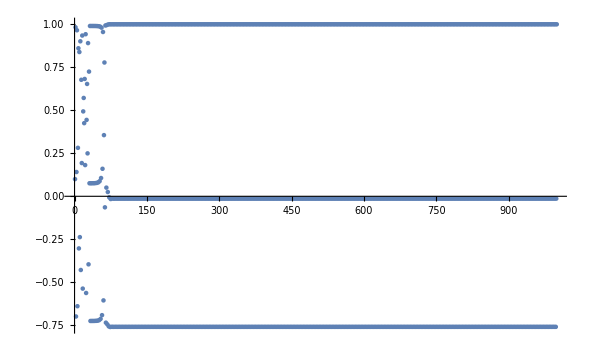

```mathematica
ListPlot[seq3]
```

```mathematica
Table[seq3[[i]],{i,200,253}]
```

{-0.758864,-0.0135402,0.999677,-0.758864,-0.0135402,0.999677,-0.758864,-0.0135402,0.999677,-0.758864,-0.0135402,0.999677,-0.758864,-0.0135402,0.999677,-0.758864,-0.0135402,0.999677,-0.758864,-0.0135402,0.999677,-0.758864,-0.0135402,0.999677,-0.758864,-0.0135402,0.999677,-0.758864,-0.0135402,0.999677,-0.758864,-0.0135402,0.999677,-0.758864,-0.0135402,0.999677,-0.758864,-0.0135402,0.999677,-0.758864,-0.0135402,0.999677,-0.758864,-0.0135402,0.999677,-0.758864,-0.0135402,0.999677,-0.758864,-0.0135402,0.999677,-0.758864,-0.0135402,0.999677}

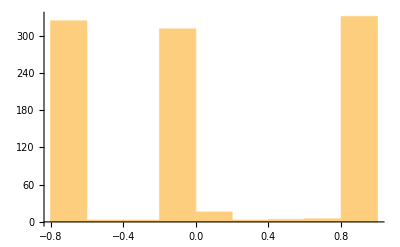

```mathematica
Histogram[seq3]
```

```mathematica
seq4 = RecurrenceTable[{a4[n+1]==1-μ*a4[n]^2,a4[1]==0.1}/.μ->1.77,a4,{n,1,1000}];
```

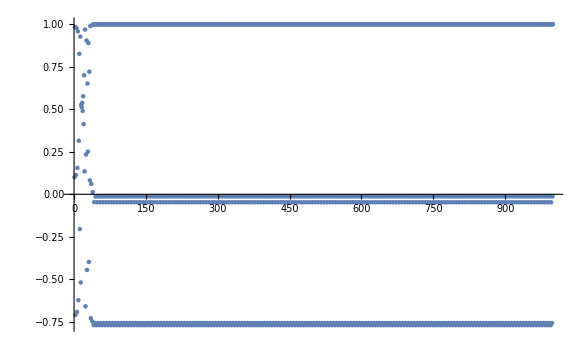

```mathematica
ListPlot[seq4]
```

```mathematica
Table[seq4[[i]],{i,200,253}]
```

{-0.756309,-0.0124471,0.999726,-0.769029,-0.0467889,0.996125,-0.756309,-0.0124471,0.999726,-0.769029,-0.0467889,0.996125,-0.756309,-0.0124471,0.999726,-0.769029,-0.0467889,0.996125,-0.756309,-0.0124471,0.999726,-0.769029,-0.0467889,0.996125,-0.756309,-0.0124471,0.999726,-0.769029,-0.0467889,0.996125,-0.756309,-0.0124471,0.999726,-0.769029,-0.0467889,0.996125,-0.756309,-0.0124471,0.999726,-0.769029,-0.0467889,0.996125,-0.756309,-0.0124471,0.999726,-0.769029,-0.0467889,0.996125,-0.756309,-0.0124471,0.999726,-0.769029,-0.0467889,0.996125}

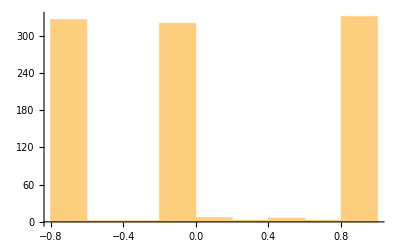

```mathematica
Histogram[seq4]
```

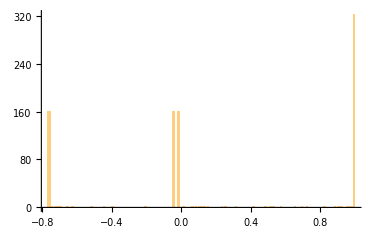

```mathematica
Histogram[seq4,200]
```

```mathematica
seq5 = RecurrenceTable[{a5[n+1]==1-μ*a5[n]^2,a5[1]==0.1}/.μ->1.78,a5,{n,1,1000}];
```

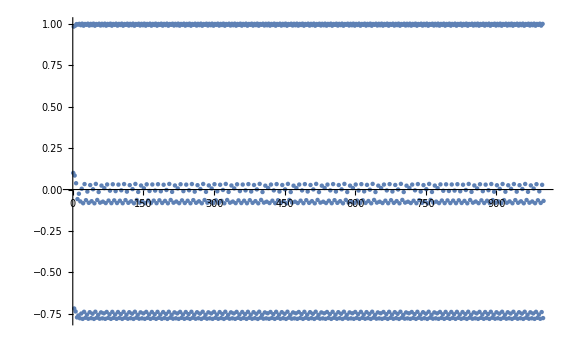

```mathematica
ListPlot[seq5]
```

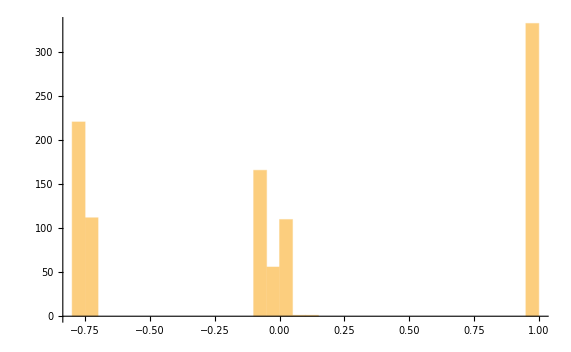

```mathematica
Histogram[seq5,30]
```

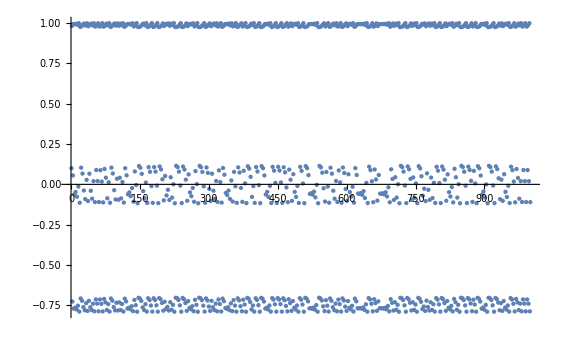

```mathematica
seq6 = RecurrenceTable[{a6[n+1]==1-μ*a6[n]^2,a6[1]==0.1}/.μ->1.79,a6,{n,1,1000}];
ListPlot[seq6]
```

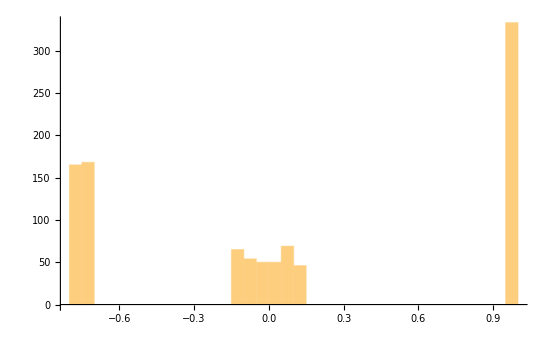

```mathematica
Histogram[seq6,30]
```

```mathematica
seq7 = RecurrenceTable[{a7[n+1]==1-μ*a7[n]^2,a7[1]==0.1}/.μ->1.80,a7,{n,1,1000}];
```

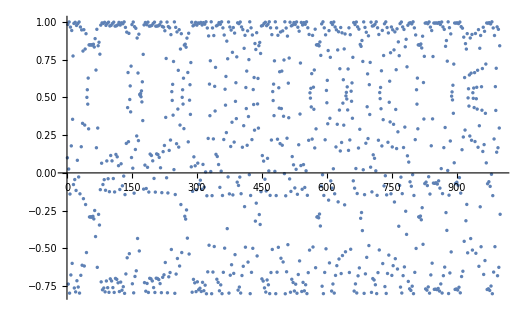

```mathematica
ListPlot[seq7]
```

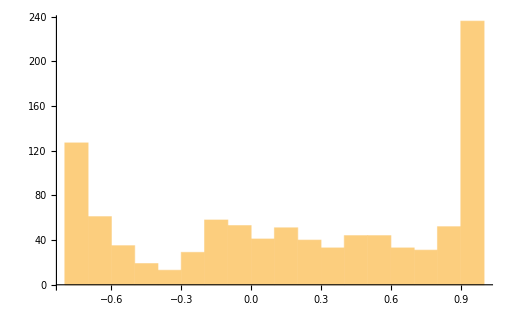

```mathematica
Histogram[seq7,20]
```

```mathematica
seq8= RecurrenceTable[{a8[n+1]==1-μ*a8[n]^2,a8[1]==1}/.μ->1.81,a8,{n,1,1000}];
```

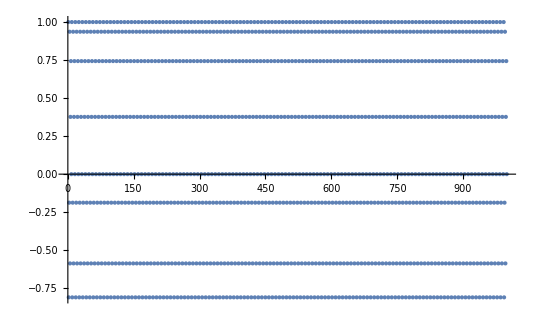

```mathematica
ListPlot[seq8]
```

```mathematica
Table[seq8[[i]],{i,200,253}]
```

{-0.0000812803,1.,-0.81,-0.187541,0.936339,-0.586884,0.376576,0.743324,-0.0000812803,1.,-0.81,-0.187541,0.936339,-0.586884,0.376576,0.743324,-0.0000812803,1.,-0.81,-0.187541,0.936339,-0.586884,0.376576,0.743324,-0.0000812803,1.,-0.81,-0.187541,0.936339,-0.586884,0.376576,0.743324,-0.0000812803,1.,-0.81,-0.187541,0.936339,-0.586884,0.376576,0.743324,-0.0000812803,1.,-0.81,-0.187541,0.936339,-0.586884,0.376576,0.743324,-0.0000812803,1.,-0.81,-0.187541,0.936339,-0.586884}

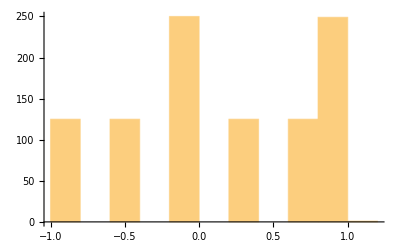

```mathematica
Histogram[seq8]
```

```mathematica
f2[x_,μ_]=f[y,μ]/.y->f[x,μ]
```

1-μ (1-x^2 μ)^2

```mathematica
Manipulate[Plot[{x,f2[x,μ]},{x,-10,10},PlotRange->{-10,10}],{μ,1/4,2}];
```

```mathematica
f3[x_,μ_]=f2[y,μ]/.y->f[x,μ]
```

1-μ (1-μ (1-x^2 μ)^2)^2

```mathematica
Manipulate[Plot[{x,f3[x,μ]},{x,-5,5},PlotRange->{-10,10}],{μ,1/4,2}];
```

```mathematica
f4[x_,μ_]=f3[y,μ]/.y->f[x,μ]
```

1-μ (1-μ (1-μ (1-x^2 μ)^2)^2)^2

```mathematica
Manipulate[Plot[{x,f4[x,μ]},{x,-5,5},PlotRange->{-10,10}],{μ,1/4,2}];
```

```mathematica
f5[x_,μ_]=f4[y,μ]/.y->f[x,μ]
```

1-μ (1-μ (1-μ (1-μ (1-x^2 μ)^2)^2)^2)^2

```mathematica
Manipulate[Plot[{x,f5[x,μ]},{x,-5,5},PlotRange->{-5,5}],{μ,1/4,2}];
```

```mathematica
f6[x_,μ_]=f5[y,μ]/.y->f[x,μ]
```

1-μ (1-μ (1-μ (1-μ (1-μ (1-x^2 μ)^2)^2)^2)^2)^2

```mathematica
Manipulate[Plot[{x,f6[x,μ]},{x,-5,5},PlotRange->{-5,5}],{μ,1/4,2}]
```

```mathematica
eq1 =g-x*y^2
```

g-x y^2

```mathematica
eq1/.y->(y1+y0)
```

g-x (y0+y1)^2

```mathematica
%/.x->(x1+x0)
```

g-(x0+x1) (y0+y1)^2

```mathematica
%//Simplify
```

g-(x0+x1) (y0+y1)^2

```mathematica
Expand[g-(x0+x1) (y0+y1)^2]
```

g-x0 y0^2-x1 y0^2-2 x0 y0 y1-2 x1 y0 y1-x0 y1^2-x1 y1^2

```mathematica
g-x0 y0^2-x1 y0^2-2 x0 y0 y1
```

g-x0 y0^2-x1 y0^2-2 x0 y0 y1

```mathematica
g-x0 y0^2-x1 y0^2-2 x0 y0 y1/.x0->h^2/g /.y0->g/h
```

-(g^2 x1)/h^2-2 h y1

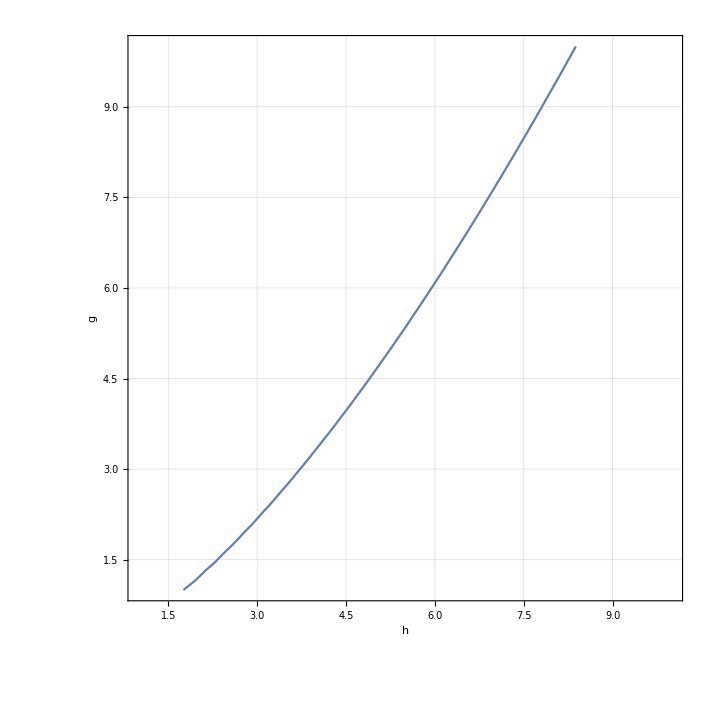

```mathematica
ff1 =ContourPlot[g^2/h^2-6*(g^2/h)+h^2==0,{h,1,10},{g,1,10},GridLines->Automatic,AxesLabel->Automatic]
```

```mathematica
Reduce[{g^2/h^2-6*(g^2/h)+h^2>0,g>1,h>1},Reals]
```

h>Root[1-6 #1+#1^4&,2]&&1<g<√(h^4/(-1+6 h))

```mathematica
Discr[h_,g_]=g^2/h^2-6*(g^2/h)+h^2
```

g^2/h^2-(6 g^2)/h+h^2

```mathematica
Discr[2,4]
```

-40

```mathematica
Discr[4,2]
```

41/4

```mathematica
Trace1 [h_,g_]= -g^2/h^2+h
```

-g^2/h^2+h

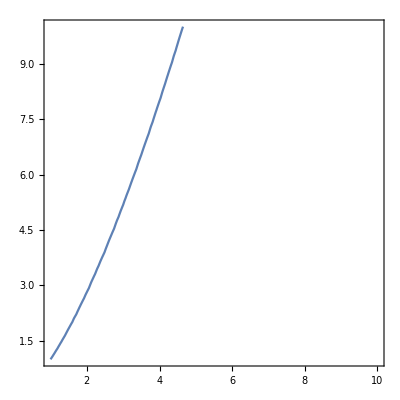

```mathematica
ff2 =ContourPlot[-g^2/h^2+h==0,{h,1,10},{g,1,10}]
```

```mathematica
-g^2/h^2+h/.h->2/.g->4
```

-2

```mathematica
-g^2/h^2+h/.h->4/.g->2
```

15/4

```mathematica
Det[({{a-λ, b}, {c, d-λ}})]
```

-b c+a d-a λ-d λ+λ^2

```mathematica
A=({{a, b}, {c, d}})
```

{{a,b},{c,d}}

```mathematica
Det[A]
```

-b c+a d

```mathematica
Det[A-λ*IdentityMatrix[2]]
```

-b c+a d-a λ-d λ+λ^2

```mathematica
Solve[-b c+a d-a λ-d λ+λ^2==0,λ]
```

{{λ→1/2 (a+d-√(a^2+4 b c-2 a d+d^2))},{λ→1/2 (a+d+√(a^2+4 b c-2 a d+d^2))}}

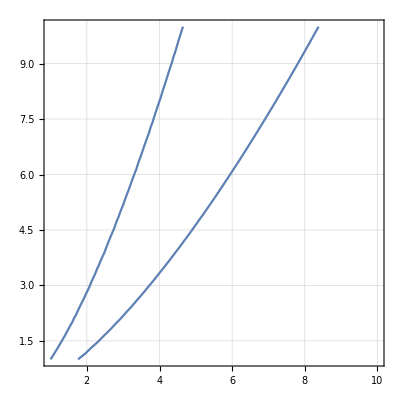

```mathematica
Show[{ff1,ff2}]
```

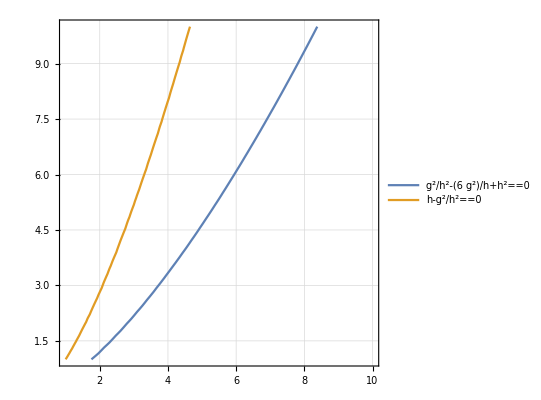

```mathematica
ContourPlot[{g^2/h^2-6*(g^2/h)+h^2==0,-g^2/h^2+h==0},{h,1,10},{g,1,10},GridLines->Automatic,PlotLegends->"Expressions"]
```

```mathematica
ContourPlot[Sqrt[g^2/h^2-6*(g^2/h)+h^2]==-g^2/h^2+h,{h,1,10},{g,1,10},GridLines->Automatic,AxesLabel->Automatic]
```

-Graphics-

```mathematica
Clear[A]
```

```mathematica
A=({{-g^2/h^2, -2h}, {g^2/h^2, h}})
```

{{-g^2/h^2,-2 h},{g^2/h^2,h}}

```mathematica
MatrixForm[A]
```

(-g^2/h^2 | -2 h
g^2/h^2 | h)

```mathematica
eq222 =CharacteristicPolynomial[A,λ]
```

g^2/h+(g^2 λ)/h^2-h λ+λ^2

# LOOK HERE

```mathematica
TraceA[h_,g_] = -g^2/h^2+h
```

-g^2/h^2+h

```mathematica
Discrim[h_,g_]= (g^2/h^2-h )^2-4*g^2/h
```

(g^2/h^2-h)^2-(4 g^2)/h

```mathematica
Dfig=ContourPlot[Discrim[h,g]==0,{h,1,10},{g,1,10},PlotLegends->{"Discriminant"},AxesLabel->Automatic,GridLines->Automatic,ContourStyle->{Red}]
```

```mathematica
Tfig = ContourPlot[TraceA[h,g]==0,{h,1,10},{g,1,10},PlotLegends->{"Trace"},AxesLabel->Automatic,GridLines->Automatic,ContourStyle->{Purple}];
```

```mathematica
Reduce[TraceA[h,g]>Discrim[h,g]]
```

(0<h<1&&-√(1/2 (-h^2+6 h^3)+1/2 √(h^4-8 h^5+32 h^6))<g<√(1/2 (-h^2+6 h^3)+1/2 √(h^4-8 h^5+32 h^6)))||(h≥1&&(-√(1/2 (-h^2+6 h^3)+1/2 √(h^4-8 h^5+32 h^6))<g<-√(1/2 (-h^2+6 h^3)-1/2 √(h^4-8 h^5+32 h^6))||√(1/2 (-h^2+6 h^3)-1/2 √(h^4-8 h^5+32 h^6))<g<√(1/2 (-h^2+6 h^3)+1/2 √(h^4-8 h^5+32 h^6))))

```mathematica
Rfig = RegionPlot[√(1/2 (-h^2+6 h^3)-1/2 √(h^4-8 h^5+32 h^6))<g<√(1/2 (-h^2+6 h^3)+1/2 √(h^4-8 h^5+32 h^6)),{h,1,10},{g,1,10},PlotLegends->{"Tr>Disc"}];
```

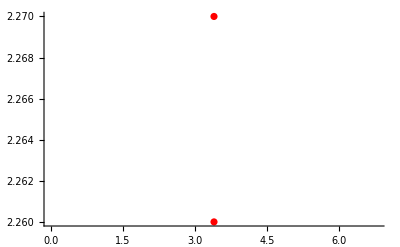

```mathematica
fft=ListPlot[{{3.4,2.26},{3.4,2.27}},PlotStyle->{Red}]
```

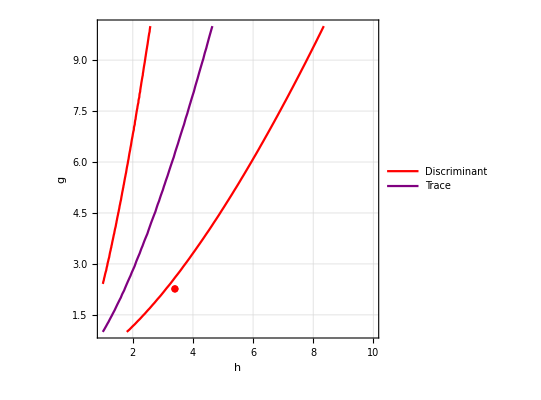

```mathematica
Show[{Dfig,Tfig,fft}]
```

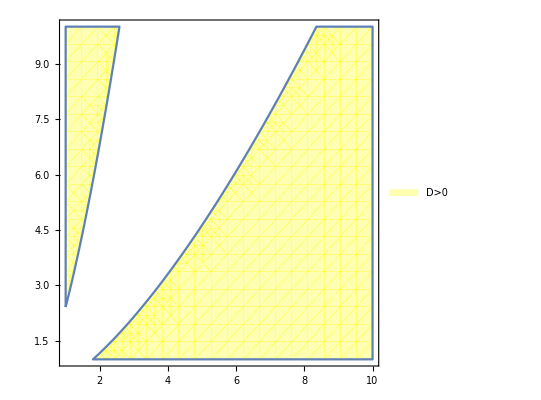

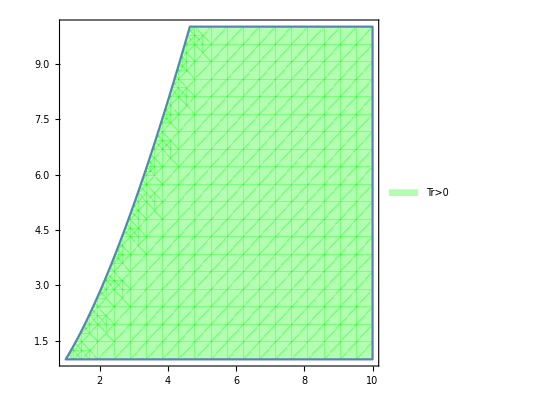

```mathematica
DGT0=RegionPlot[Discrim[h,g]>0,{h,1,10},{g,1,10},PlotStyle->{Yellow,Opacity[0.3]},PlotLegends->{"D>0"}]
TGT0=RegionPlot[TraceA[h,g]>0,{h,1,10},{g,1,10},PlotStyle->{Green,Opacity[0.3]},PlotLegends->{"Tr>0"}]
```

```mathematica
TraceA[2,8]+Sqrt[Discrim[2,8]]
```

-14+2 √17

```mathematica
N[-14+2 √17]
```

-5.75379

```mathematica
N[TraceA[1,6]+Sqrt[Discrim[1,6]]]
```

-2.12144

```mathematica
Reduce[TraceA[h,g]+Sqrt[Discrim[h,g]]>0]
```

(h<0&&(g<0||g>0))||(h>0&&-√(3 h^3-2 √2 √(h^6))≤g≤√(3 h^3-2 √2 √(h^6)))

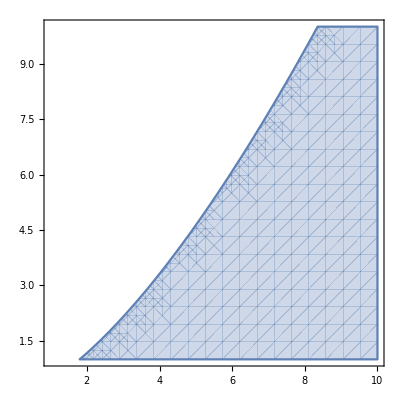

```mathematica
RegionPlot[-√(3 h^3-2 √2 √(h^6))≤g≤√(3 h^3-2 √2 √(h^6)),{h,1,10},{g,1,10}]
```

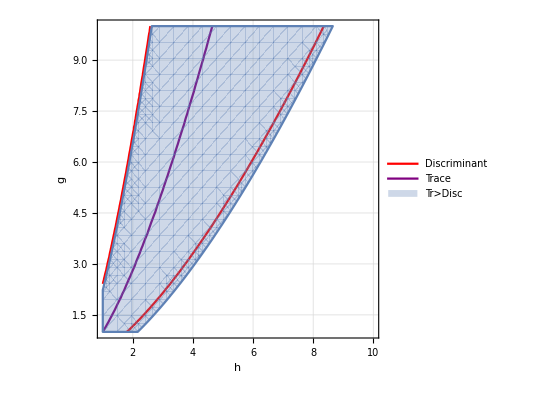

```mathematica
Show[{Dfig,Tfig,Rfig}]
```

```mathematica
eq2[2,8]
```

68

```mathematica
eq2[4,4]
```

-7

```mathematica
eq2[6,2]
```

2593/81

```mathematica
eq11[2,4]
```

-2

```mathematica
eq11[4,2]
```

15/4

```mathematica
eq11[8,2]
```

127/16

```mathematica
N[127/16]
```

7.9375

```mathematica
eq2[8,2]
```

15617/256

```mathematica
Sqrt[15617/256]
```

(√15617)/16

```mathematica
N[(√15617)/16]
```

7.8105

```mathematica
Sqrt[61]
```

√61

```mathematica
N[√61]
```

7.81025

```mathematica
Reduce[eq11[h,g]>Sqrt[eq2[h,g]]]
```

h>0&&(-√(3 h^3-2 √2 √(h^6))≤g<0||0<g≤√(3 h^3-2 √2 √(h^6)))

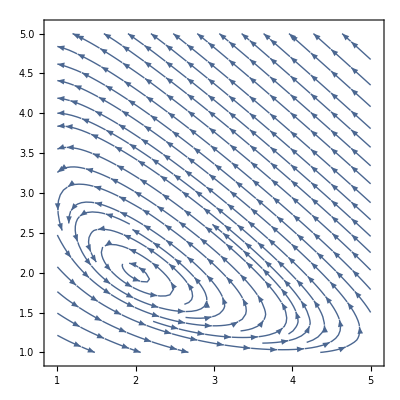

```mathematica
StreamPlot[{8-x*y^2,-4y+x*y^2},{x,1,5},{y,1,5}]
```

```mathematica
Solve[TraceA[4,g]==0,g]
```

{{g→-8},{g→8}}

```mathematica
NDSolve[{x'[t]==3.4-x[t]*(y[t])^2,y'[t]==-2.26*y[t]+x[t]*(y[t])^2,x[0]==1.1,y[0]==1.2},{x[t],y[t]},t]
```

NDSolve::ndlim: Range specification t is not of the form {x, xend} or {x, xmin, xmax}.

{{x[t]→InterpolatingFunction[{{0., 0.}}, <>][t],y[t]→InterpolatingFunction[{{0., 0.}}, <>][t]}}

```mathematica
sol=NDSolve[{x'[t]==3.4-x[t]*(y[t])^2,y'[t]==-2.26*y[t]+x[t]*(y[t])^2,x[0]==1.1,y[0]==1.2},{x,y},{t,200}]
```

{{x→InterpolatingFunction[{{0., 200.}}, <>],y→InterpolatingFunction[{{0., 200.}}, <>]}}

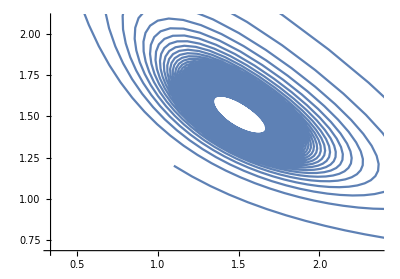

```mathematica
ParametricPlot[Evaluate[{x[t],y[t]}/.sol],{t,0,200}]
```

```mathematica
solx[t]=sol[[1,1]]
```

x→InterpolatingFunction[{{0., 250.}}, <>]

```mathematica
sol[[1,2]]
```

y→InterpolatingFunction[{{0., 250.}}, <>]

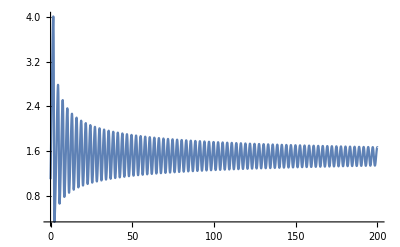

```mathematica
Plot[Evaluate[x[t]/.sol[[1,1]]],{t,0,200},PlotRange->All]
```

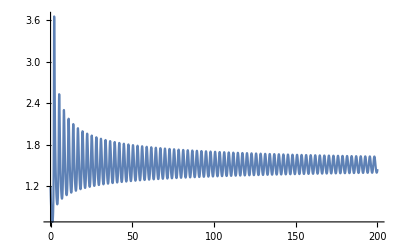

```mathematica
Plot[Evaluate[y[t]/.sol[[1,2]]],{t,0,200},PlotRange->All]
```

```mathematica
sol2=NDSolve[{x'[t]==3.4-x[t]*(y[t])^2,y'[t]==-2.27*y[t]+x[t]*(y[t])^2,x[0]==1.1,y[0]==1.2},{x,y},{t,200}]
```

{{x→InterpolatingFunction[{{0., 200.}}, <>],y→InterpolatingFunction[{{0., 200.}}, <>]}}

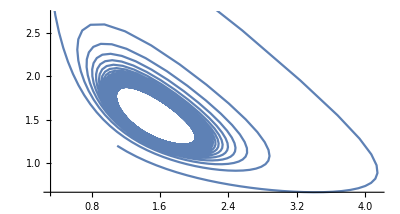

```mathematica
ParametricPlot[Evaluate[{x[t],y[t]}/.sol2],{t,0,200}]
```

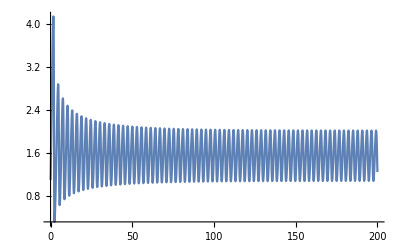

```mathematica
Plot[Evaluate[x[t]/.sol2[[1,1]]],{t,0,200},PlotRange->All]
```

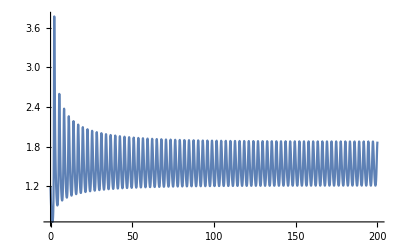

```mathematica
Plot[Evaluate[y[t]/.sol2[[1,2]]],{t,0,200},PlotRange->All]
```